# 1+1 d box, ϕ^3 field

Consider a scalar field satisfying a1+1 d wave equation with a ϕ^3 interaction. The domain is a box of size l, with reflecting boundary conditions.

- \partial^2_t \phi + \partial^2_x \phi = \lambda \phi^3

## TTF Equations

### Normal modes

```mathematica
(* Frequency and wavefunction *) 
ω[j_]:=π j/l
f[j_,x_]:=Sqrt[2/l]Sin[ω[j]x]
```

```mathematica
(* Check orthonormality *)
Integrate[f[n,x]f[m,x],{x,0,l},Assumptions->{m∈Integers,m>0,n∈Integers,n>0}]
```

(2 n Cos[n π] Sin[m π]-2 m Cos[m π] Sin[n π])/(m^2 π-n^2 π)

```mathematica
FullSimplify[%,]
```

-(2 (-1)^m m Sin[n π])/(m^2 π-n^2 π)

```mathematica
Limit[%17,n ->m]
```

(-1)^m m DirectedInfinity[Sign[Sin[m π]]/Sign[m]]

### Overlap integrals

```mathematica
Integrate[f[n,x]f[p,x]f[q,x]f[r,x],{x,0,l}]//Expand
```

$Aborted

```mathematica
Expand[%10]
```

1-Sin[2 m π]/(2 m π)

```mathematica
μ[n_,p_,q_,r_]:=λ/(2l)(-KroneckerDelta[n-p-q-r,0]+KroneckerDelta[n+p-q-r,0]+KroneckerDelta[n-p+q-r,0]-KroneckerDelta[n+p+q-r,0]+KroneckerDelta[n-p-q+r,0]-KroneckerDelta[n+p-q+r,0]-KroneckerDelta[n-p+q+r,0]+KroneckerDelta[n+p+q+r,0])
```

```mathematica
λ=1;l=1;
```

```mathematica
max=20;
```

```mathematica
eqs=Table[-2ⅈ ω[n]D[A[n][τ],τ]==Sum[μ[n,p,q,r](-A[p][τ]A[q][τ]A[r][τ]KroneckerDelta[0,n-p-q-r]+A[p][τ]A[q][τ]Conjugate[A[r][τ]]KroneckerDelta[0,n-p-q+r]+A[p][τ]Conjugate[A[q][τ]]A[r][τ]KroneckerDelta[0,n-p+q-r]-A[p][τ]Conjugate[A[q][τ]]Conjugate[A[r][τ]]KroneckerDelta[0,n-p+q+r]+Conjugate[A[p][τ]]A[q][τ]A[r][τ]KroneckerDelta[0,n+p-q-r]-Conjugate[A[p][τ]]A[q][τ]Conjugate[A[r][τ]]KroneckerDelta[0,n+p-q+r]-Conjugate[A[p][τ]]Conjugate[A[q][τ]]A[r][τ]KroneckerDelta[0,n+p+q-r]+Conjugate[A[p][τ]]Conjugate[A[q][τ]]Conjugate[A[r][τ]]KroneckerDelta[0,n+p+q+r]),{p,1,max},{q,1,max},{r,1,max}],{n,1,max}];
```

### Conservation of E

```mathematica
derivs=Solve[eqs,Table[A[n]'[τ],{n,1,max}]][[1]];
```

```mathematica
dEdt=Sum[ω[n]^2(A[n]'[τ]Conjugate[A[n][τ]]+A[n][τ]Conjugate[A[n]'[τ]]),{n,1,max}];
```

```mathematica
dEdt//.derivs//FullSimplify
```

0

### Numerical solutions

```mathematica
vbls=Table[A[j],{j,1,max}];
```

```mathematica
initial=Table[A[j][0]==Switch[j,1,1,3,0.01441,5,0.000204875,_,0],{j,1,max}];
```

```mathematica
tmax=100;
sol=NDSolve[Join[eqs,initial],vbls,{τ,0,tmax},Method->{"EquationSimplification"->"Solve","TimeIntegration"->{"ImplicitRungeKutta","DifferenceOrder"->6}}]
```

{{A[1]→InterpolatingFunction[{{0., 100.}}, <>],A[2]→InterpolatingFunction[{{0., 100.}}, <>],A[3]→InterpolatingFunction[{{0., 100.}}, <>],A[4]→InterpolatingFunction[{{0., 100.}}, <>],A[5]→InterpolatingFunction[{{0., 100.}}, <>],A[6]→InterpolatingFunction[{{0., 100.}}, <>],A[7]→InterpolatingFunction[{{0., 100.}}, <>],A[8]→InterpolatingFunction[{{0., 100.}}, <>],A[9]→InterpolatingFunction[{{0., 100.}}, <>],A[10]→InterpolatingFunction[{{0., 100.}}, <>],A[11]→InterpolatingFunction[{{0., 100.}}, <>],A[12]→InterpolatingFunction[{{0., 100.}}, <>],A[13]→InterpolatingFunction[{{0., 100.}}, <>],A[14]→InterpolatingFunction[{{0., 100.}}, <>],A[15]→InterpolatingFunction[{{0., 100.}}, <>],A[16]→InterpolatingFunction[{{0., 100.}}, <>],A[17]→InterpolatingFunction[{{0., 100.}}, <>],A[18]→InterpolatingFunction[{{0., 100.}}, <>],A[19]→InterpolatingFunction[{{0., 100.}}, <>],A[20]→InterpolatingFunction[{{0., 100.}}, <>]}}

```mathematica
plots=Table[Abs[A[j][τ]],{j,1,max}]/.sol;
```

```mathematica
plotsEtot=Sum[ω[j]^2*Abs[A[j][τ]]^2,{j,1,max}]/.sol;
plotsNtot=Sum[ω[j]*Abs[A[j][τ]]^2,{j,1,max}]/.sol;
```

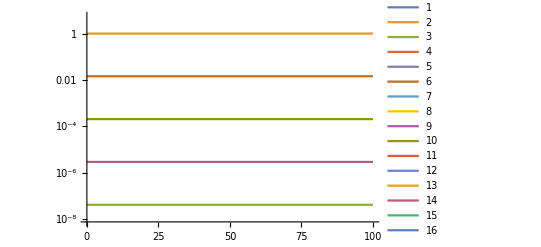

```mathematica
LogPlot[plots,{τ,0,tmax},PlotRange->All,PlotLegends->Table[j,{j,1,max}]]
```

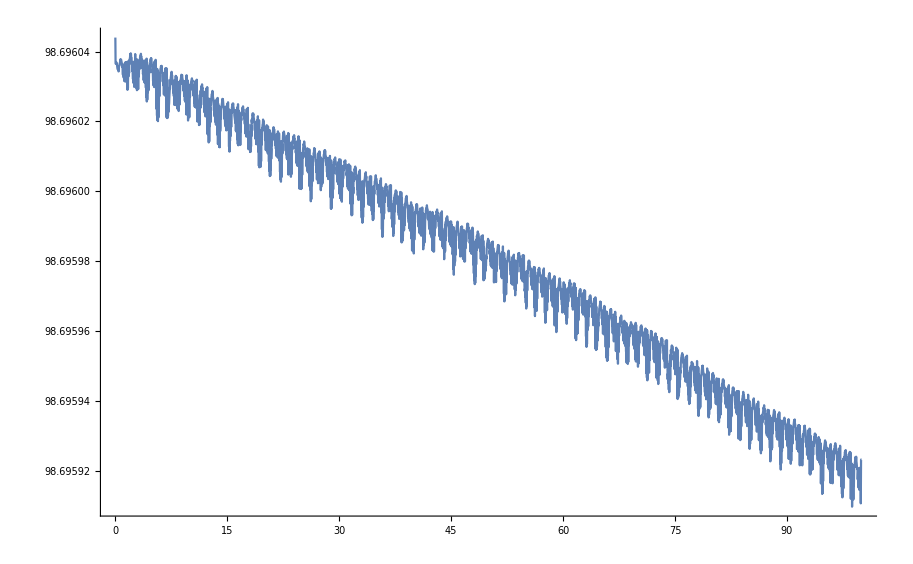

```mathematica
Plot[plotsNtot,{τ,0,tmax}]
```

### Periodic equilibria

```mathematica
temp=eqs/.{A[n_][τ_]:>α[n]Exp[-ⅈ β n τ],A[n_]'[τ_]:>-ⅈ β n α[n]Exp[-ⅈ β n τ]};
```

```mathematica
temp=Refine[temp,{β∈ Reals,τ∈Reals}];
```

```mathematica
temp=Table[Expand[temp[[n,1]]Exp[ⅈ β n τ]]==Expand[temp[[n,2]]Exp[ⅈ β n τ]],{n,1,max}];
```

#### Choice of first mode n=1

```mathematica
firstmode=1;
allowedmodes=Range[firstmode,max,2firstmode];
excludedmodes=Complement[Range[max],allowedmodes];
```

```mathematica
reducedEqs=temp[[allowedmodes]]/.((α[#]->0)&/@excludedmodes);
```

```mathematica
root=FindRoot[reducedEqs/.α[1]->1,Join[{{α[3],.01},{α[5],.001}},({α[#],0})&/@allowedmodes[[4;;-1]],{{β,0}}]]
```

{α[3]→0.0144163,α[5]→0.000204917,α[7]→2.91275×10^-6,α[9]→4.14025×10^-8,α[11]→5.88507×10^-10,α[13]→8.36519×10^-12,α[15]→1.18905×10^-13,α[17]→1.69015×10^-15,α[19]→2.40239×10^-17,β→-0.719839}

```mathematica
psol=Join[{α[firstmode]->1},root[[1;;-2]],{α[n_]:>0}]
```

{α[1]→1,α[3]→0.0144163,α[5]→0.000204917,α[7]→2.91275×10^-6,α[9]→4.14025×10^-8,α[11]→5.88507×10^-10,α[13]→8.36519×10^-12,α[15]→1.18905×10^-13,α[17]→1.69015×10^-15,α[19]→2.40239×10^-17,α[n_]:>0}

```mathematica
initial=Table[A[j][0]==α[j],{j,1,max}]/.psol
```

{A[1][0]==1,A[2][0]==0,A[3][0]==0.0144163,A[4][0]==0,A[5][0]==0.000204917,A[6][0]==0,A[7][0]==2.91275×10^-6,A[8][0]==0,A[9][0]==4.14025×10^-8,A[10][0]==0,A[11][0]==5.88507×10^-10,A[12][0]==0,A[13][0]==8.36519×10^-12,A[14][0]==0,A[15][0]==1.18905×10^-13,A[16][0]==0,A[17][0]==1.69015×10^-15,A[18][0]==0,A[19][0]==2.40239×10^-17,A[20][0]==0}

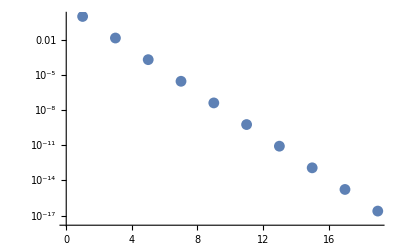

```mathematica
ListLogPlot[initial[[All,2]]]
```

#### Choice of first mode n=2

```mathematica
firstmode=2;
allowedmodes=Range[firstmode,max,2firstmode];
excludedmodes=Complement[Range[max],allowedmodes];
```

```mathematica
reducedEqs=temp[[allowedmodes]]/.((α[#]->0)&/@excludedmodes);
```

```mathematica
root=FindRoot[reducedEqs/.α[2]->1,Join[{{α[6],.01},{α[10],.001}},({α[#],0})&/@allowedmodes[[4;;-1]],{{β,0}}]]
```

{α[6]→0.0144163,α[10]→0.000204917,α[14]→2.91275×10^-6,α[18]→4.14×10^-8,β→-0.17996}

```mathematica
psol=Join[{α[firstmode]->1},root[[1;;-2]],{α[n_]:>0}]
```

{α[2]→1,α[6]→0.0144163,α[10]→0.000204917,α[14]→2.91275×10^-6,α[18]→4.14×10^-8,α[n_]:>0}

```mathematica
initial=Table[A[j][0]==α[j],{j,1,max}]/.psol
```

{A[1][0]==0,A[2][0]==1,A[3][0]==0,A[4][0]==0,A[5][0]==0,A[6][0]==0.0144163,A[7][0]==0,A[8][0]==0,A[9][0]==0,A[10][0]==0.000204917,A[11][0]==0,A[12][0]==0,A[13][0]==0,A[14][0]==2.91275×10^-6,A[15][0]==0,A[16][0]==0,A[17][0]==0,A[18][0]==4.14×10^-8,A[19][0]==0,A[20][0]==0}

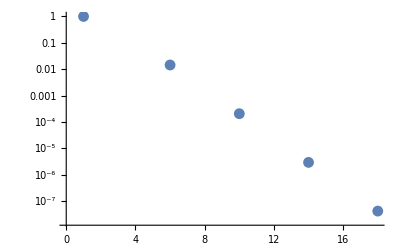

```mathematica
ListLogPlot[initial[[All,2]]]
```